## CP9: Non-linear dynamical systems

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Non-linear dynamical systems of ODEs and REs

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

### 9-1: Non-linear system of differential equations

Consider the following system of ODEs: ⅆx/ⅆt=8x-y^2, ⅆy/ⅆt=x^2-y

(a) Calculate the equilibria of this system.

```mathematica
sys1={D[x[t],t]==8x[t]-(y[t])^2, D[y[t],t]==(x[t])^2-y[t]}
f1=8*x-y^2;
g1=x^2-y;
eq1=Values[NSolve[f1==0&&g1==0,{x,y}]]
eq1=Values[NSolve[f1==0&&g1==0,{x,y}, Reals]]
```

{x'[t]==8 x[t]-y[t]^2,y'[t]==x[t]^2-y[t]}

{{2.,4.},{-1.+1.73205 ⅈ,-2.-3.4641 ⅈ},{-1.-1.73205 ⅈ,-2.+3.4641 ⅈ},{0.,0.}}

{{2.,4.},{0.,0.}}

(b) Calculate the Jacobian for each of the real equilibria in (a).

```mathematica
j1=D[{f1, g1}, {{x,y}}];
MatrixForm[j1]
```

(8 | -2 y
2 x | -1)

```mathematica
j1eq1=Table[j1/.{x->eq1[[k,1]], y->eq1[[k,2]]}, {k, 1, Length[eq1]}]
```

{{{8,-8.},{4.,-1}},{{8,0.},{0.,-1}}}

(c) Use the Jacobians from (b) to assess the properties of the equilibria.

```mathematica
evalEq[j_]:=If[Det[j]<=0.25*Tr[j]^2, If[Det[j]<0, "saddle node", If[Tr[j]<0, "stable node", "unstable node"]], If[Tr[j]==0, "centre spiral", If[Tr[j]<0,"stable spiral", "unstable spiral"]]]
Table[evalEq[j1eq1[[k]]], {k, 1, Length[eq1]}]
```

{unstable spiral,saddle node}

(d) Solve the system numerically for initial values {x,y}={2.01,4.01} and plot the solutions in a time plot and a phase plot.

```mathematica
init1={x[0]==2.01, y[0]==4.01};
maxT=2;
sol1=NDSolveValue[{sys1, init},{x[t],y[t]},{t, 0,maxT}];
```

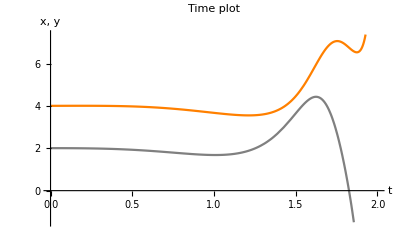

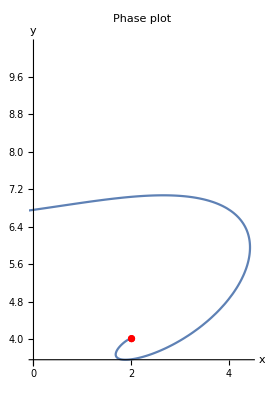

```mathematica
tp=Plot[sol1, {t, 0,maxT},PlotLabel->"Time plot",AxesLabel->{"t","x, y"},PlotStyle->{Gray,Orange}]
pp=ParametricPlot[sol1, {t, 0,maxT}, PlotLabel->"Phase plot", AxesLabel->{"x","y"}];
ip=ListPlot[{{2.01,4.01}}, PlotStyle->Red];
Show[pp,ip]
```

(e) Plot a phase portrait of the system for initial values {x,y}={2.01,4.01}, {0.01,0}, {-0.01,0}, {6,-10}, {7,-10}.

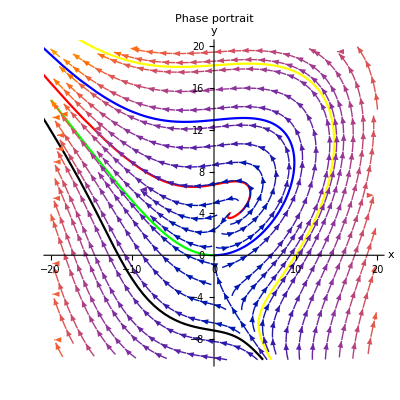

```mathematica
init2={x[0]==0.01,y[0]==0.0};
init3={x[0]==-0.01,y[0]==0.0};
init4={x[0]==6.,y[0]==-10.};
init5={x[0]==7.,y[0]==-10.};
sol2=NDSolveValue[{sys1,init2},{x[t],y[t]},{t,0,1.1}];
sol3=NDSolveValue[{sys1,init3},{x[t],y[t]},{t,0,0.9}];
sol4=NDSolveValue[{sys1,init4},{x[t],y[t]},{t,0,0.4}];
sol5=NDSolveValue[{sys1,init5},{x[t],y[t]},{t,0,0.4}];
p1=ParametricPlot[{sol1,sol2},{t,0,2},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Red,Blue},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"x","y"}];
p2=ParametricPlot[sol3,{t,0,.9},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Green}];
p3=ParametricPlot[{sol4,sol5},{t,0,.4},PlotRange->{{-20,20},{-10,20}},PlotStyle->{Black,Yellow}];
Show[p1,p2,p3,StreamPlot [{f1,g1},{x,-20,20},{y,-10,20},StreamScale->{Tiny,Automatic,0.01}, StreamStyle->Pink]]
```

### 9-2: 2-species competition model

Consider the following system of differential equations describing competition between two species N_1 and N_2: (ⅆ N_1)/ⅆt=N_1(r_1-a_11 N_1-a_12 N_2), (ⅆ N_2)/ⅆt=N_2(r_2-a_21 N_1-a_22 N_2). For your analysis, use the specific values r_1=4, r_2=8, a_11=a_12=a_22=1, a_21=3.

(a) Calculate the four equilibria of the system.

```mathematica
sp1=N1*(4-N1-N2);
sp2=N2*(8-3N1-N2);
eq=Values[Solve[sp1==0  && sp2==0, {N1, N2}, Reals]]
```

{{0,0},{0,8},{2,2},{4,0}}

(b) Calculate the Jacobian for each equilibrium in (a)

```mathematica
j=D[{sp1,sp2},{{N1,N2}}]
jEq=Table[j/.{N1->eq[[k,1]], N2->eq[[k,2]]},{k,1,Length[eq]}]
```

{{4-2 N1-N2,-N1},{-3 N2,8-3 N1-2 N2}}

{{{4,0},{0,8}},{{-4,0},{-24,-8}},{{-2,-2},{-6,-2}},{{-4,-4},{0,-4}}}

(c) Which equilibria are stable and which are unstable? Do you expect oscillations?

```mathematica
Table[evalEq[jEq[[k]]],{k,1,Length[eq]}]
```

{unstable node,stable node,saddle node,stable node}

(d) Solve the system numerically for initial values {N1(0),N2(0)}={3.99,0.0} and plot the solutions in a time plot and a phase plot.

```mathematica
sys2={D[N1[t],t]==N1[t]*(4-N1[t]-N2[t]), D[N2[t],t]==N2[t]*(8-3N1[t]-N2[t])}
```

{N1'[t]==N1[t] (4-N1[t]-N2[t]),N2'[t]==(8-3 N1[t]-N2[t]) N2[t]}

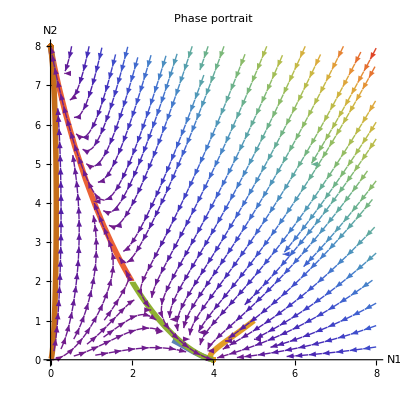

```mathematica
init1={N1[0]==3.0, N2[0]==0.5};
init2={N1[0]==5.0,N2[0]==1.0};
init3a={N1[0]==2.01,N2[0]==1.99};
init3b={N1[0]==1.99,N2[0]==2.01};
init4={N1[0]==0.1,N2[0]==7};
init5={N1[0]==0.01,N2[0]==0.01};
sol1=NDSolveValue[{sys2,init1},{N1[t],N2[t]},{t,0,10}];
sol2=NDSolveValue[{sys2,init2},{N1[t],N2[t]},{t,0,10}];
sol3a=NDSolveValue[{sys2,init3a},{N1[t],N2[t]},{t,0,10}];
sol3b=NDSolveValue[{sys2,init3b},{N1[t],N2[t]},{t,0,10}];
sol4=NDSolveValue[{sys2,init4},{N1[t],N2[t]},{t,0,10}];
sol5=NDSolveValue[{sys2,init5},{N1[t],N2[t]},{t,0,10}];
pp=ParametricPlot[{sol1,sol2, sol3a, sol3b, sol4, sol5},{t,0,10},PlotRange->All,AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"N1","N2"}, PlotStyle->Thickness[0.01]];
Show[pp,StreamPlot [{sp1,sp2},{N1,0,8},{N2,0,8},StreamScale->{Tiny,Automatic,0.01}, StreamColorFunction->"Rainbow"]]
```

The two species cannot co-exist. Depending on the initial conditions, only one of the species could exist if it has higher initial population.

### 9-3: Host-parasite interactions: The Nicholson-Bailey model

The Nicholson-Bailey model can be described by the following system of recurrence equations: H_(t+1)=R·H_t e^-aP_t, P_(t+1)=c·H_t(1-e^-aP_t). Assume in your analysis that a=c=1.

(a) Show that the equilibrium of the system equals Ĥ=(Rln(R))/(R-1),  P̂=ln(R).

```mathematica
h=R*H*Exp[-P];
p=H*(1-Exp[-P]);
sol=Values[Solve[h==H&&p==P,{H,P}, Reals, Assumptions->R>1]]
```

{{0,0},{(R Log[R])/(-1+R),Log[R]}}

(b) Show that this equilibrium is always unstable.

```mathematica
j=D[{h,p},{{H,P}}];
MatrixForm[j]
```

(ⅇ^-P R | -ⅇ^-P H R
1-ⅇ^-P | ⅇ^-P H)

```mathematica
Eigenvalues[j]/.{H->sol[[1,1]],P->sol[[1,2]]}
Det[j]/.{H->sol[[1,1]],P->sol[[1,2]]}
Tr[j]/.{H->sol[[1,1]],P->sol[[1,2]]}
```

{1/2 (R-√(R^2)),1/2 (R+√(R^2))}

0

R

```mathematica
Eigenvalues[j]/.{H->sol[[2,1]],P->sol[[2,2]]}
Det[j]/.{H->sol[[2,1]],P->sol[[2,2]]}
Tr[j]/.{H->sol[[2,1]],P->sol[[2,2]]}
```

{ConditionalExpression[(R+(R Log[R])/(-1+R)-√(R^2+(2 R^2 Log[R])/(-1+R)-(4 R^3 Log[R])/(-1+R)+(R^2 Log[R]^2)/(-1+R)^2))/(2 R), 0<R<1||R>1],ConditionalExpression[(R+(R Log[R])/(-1+R)+√(R^2+(2 R^2 Log[R])/(-1+R)-(4 R^3 Log[R])/(-1+R)+(R^2 Log[R]^2)/(-1+R)^2))/(2 R), 0<R<1||R>1]}

ConditionalExpression[(R Log[R])/(-1+R), 0<R<1||R>1]

ConditionalExpression[1+Log[R]/(-1+R), 0<R<1||R>1]

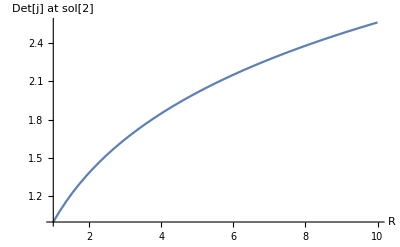

```mathematica
Plot[R*Log[R]/(R-1), {R,1,10}, AxesLabel->{"R","Det[j] at sol[2]"}]
```

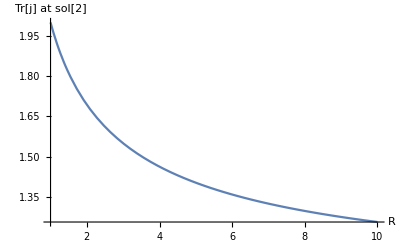

```mathematica
Plot[1+(Log[R]/(R-1)), {R,1,10}, AxesLabel->{"R","Tr[j] at sol[2]"}]
```

Here, the trace of the Jacobian matrix is always >1 for R>1. Looking at the above graph, we also see that the determinant is also always >1 for R>1.
The expectation that host-parasitoid systems are unstable is in line with many laboratory studies. In the lab, host-parasitoid systems have a strong tendency towards diverging oscillations that ultimately lead to the extinction of at least one of the populations. However, natural host-parasitoid systems are certainly more stable than indicated by the Nicholson-Bailey model. Apparently, the simple model (4) is not a satisfactory representation of real host-parasitoid systems. In order to cope with this criticism, the model has been modified repeatedly by making more realistic assumptions concerning the host and parasitoid dynamics.

(c) Use the density-dependent Nicholson-Bailey model: H_(t+1)=R·H_t e^(-bH_t-aP_t), P_(t+1)=c·H_t(1-e^-aP_t). Assume again that a=c=1. For parameter values b=0.5 and R=4, and initial values H_0=2.0 and P_0=1.0, plot the system and calculate the new equilibrium. Is the system stable and/or oscillating? Hint: Program a function in Mathematica using the command Manipulate[] to vary the values of R and b.

```mathematica
h=R*H*Exp[-1/2*H-P]
p=H*(1-Exp[-P])
h1=h/.R->4
eq=Values[Solve[h1==H && p==P, {H,P}, Reals]]
```

ⅇ^(-H/2-P) H R

(1-ⅇ^-P) H

4 ⅇ^(-H/2-P) H

{{0,0},{Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906,1/2 (4 Log[2]-Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906)},{Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781,1/2 (4 Log[2]-Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781)}}

```mathematica
j=D[{h1,p}, {{H,P}}]
jEq=Table[j/.{H->eq[[k,1]], P->eq[[k,2]]},{k,1,Length[eq]}]
```

{{4 ⅇ^(-H/2-P)-2 ⅇ^(-H/2-P) H,-4 ⅇ^(-H/2-P) H},{1-ⅇ^-P,ⅇ^-P H}}

{{{4,0},{0,0}},{{4 ⅇ^(-1/2 Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906+1/2 (-4 Log[2]+Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906))-2 ⅇ^(-1/2 Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906+1/2 (-4 Log[2]+Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906)) Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906,-4 ⅇ^(-1/2 Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906+1/2 (-4 Log[2]+Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906)) Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906},{1-ⅇ^(1/2 (-4 Log[2]+Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906)),ⅇ^(1/2 (-4 Log[2]+Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906)) Root1.39Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,1.3862943611198906188}]1.3862943611198906}},{{4 ⅇ^(-1/2 Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781+1/2 (-4 Log[2]+Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781))-2 ⅇ^(-1/2 Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781+1/2 (-4 Log[2]+Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781)) Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781,-4 ⅇ^(-1/2 Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781+1/2 (-4 Log[2]+Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781)) Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781},{1-ⅇ^(1/2 (-4 Log[2]+Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781)),ⅇ^(1/2 (-4 Log[2]+Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781)) Root2.77Root[{8 Log[2]-6 #1+ⅇ^(#1/2) #1&,2.7725887222397812377}]2.772588722239781}}}

```mathematica
(*Stable = All eigenvalues have absolute value < 1*)
Table[Abs[Eigenvalues[jEq[[1]]]][[k]]<1, {k,1,2}](*the 1st equilibrium is unstable*)
Table[Abs[Eigenvalues[jEq[[2]]]][[k]]<1, {k,1,2}] (*the 2nd equilibrium is stable*)
Table[Abs[Eigenvalues[jEq[[3]]]][[k]]<1, {k,1,2}](*the 3rd equilibrium is unstable*)
```

{False,True}

{True,True}

{False,True}

```mathematica
Table[If[Det[jEq[[k]]]>1/4*(Tr[jEq[[k]]])^2,"spiral","node"],{k,1,Length[eq]}]
```

{node,spiral,node}

```mathematica
eq1=H[t+1]==4*H[t]*Exp[-1/2*H[t]-P[t]];
eq2=P[t+1]==H[t]*(1-Exp[-P[t]]);
init={H[0]==2.0, P[0]==1.0};
```

```mathematica
pts1=RecurrenceTable[{eq1,eq2,init},{H[t],P[t]},{t,0,100}];
ListLinePlot[pts1,PlotRange->All]
```

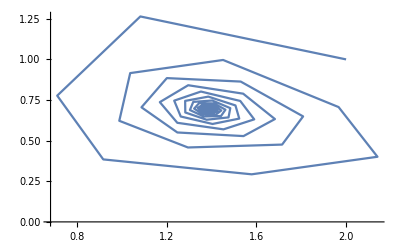

There is one stable equilibrium and the system oscillates with decreasing amplitude towards this equilibrium.

(d) Do the same for parameter values b=0.25 and R=5. Is the system stable and/or oscillating?

```mathematica
plotNicholsonBailey[p1_,p2_]:=Module[{eq1,eq2,init,t,pts, phase, initPoint},
eq1= H[t+1]==p1*H[t]*Exp[-p2*H[t]-P[t]];
eq2=P[t+1]==H[t]*(1-Exp[-P[t]]);
init={H[0]==2.0,P[0]==1.0};
pts=RecurrenceTable[{eq1,eq2,init},{H[t],P[t]},{t,0,100}];
phase=ListLinePlot[pts,PlotRange->All];
initPoint=ListPlot[{{2.0,1.0}}, PlotStyle->Red];
Show[phase, initPoint]
]
```

```mathematica
Manipulate[plotNicholsonBailey[R,b],{R,1.1,10},{b,0.0,1.0}]
```

The equilibrium becomes stable as b increases and R decreases. For larger R, larger b is required to have convergence behaviour.